# Notebook for : Weyl tensor in spatially homogeneous cosmological models by Barrow & Hervik

Geoff Cope
University of Utah
April 27th, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article

```mathematica
Hyperlink["Weyl tensor in spatially homogeneous cosmological models by Barrow & Hervik",
"https://arxiv.org/abs/gr-qc/0206061"]
```

[Weyl tensor in spatially homogeneous cosmological models by Barrow & Hervik](https://arxiv.org/abs/gr-qc/0206061)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 10 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Kasner Line Element and Metric

```mathematica
Clear[kasner]
kasner = 
-dt^2+ t^(2 p1) dx^2+ t^(2 p2) dy^2+ t^(2 p3) dz^2
```

-dt^2+dx^2 t^(2 p1)+dy^2 t^(2 p2)+dz^2 t^(2 p3)

```mathematica
Clear[kasnerMetric]
kasnerMetric = 
lineToMetric[ kasner , {dt,dx,dy,dz}]  ;
kasnerMetric // MatrixForm
```

(-1 | 0 | 0 | 0
0 | t^(2 p1) | 0 | 0
0 | 0 | t^(2 p2) | 0
0 | 0 | 0 | t^(2 p3))

```mathematica
Clear[inverseKasner]
inverseKasner = 
Inverse[ kasnerMetric ] ;
inverseKasner // MatrixForm
```

(-1 | 0 | 0 | 0
0 | t^(-2 p1) | 0 | 0
0 | 0 | t^(-2 p2) | 0
0 | 0 | 0 | t^(-2 p3))

```mathematica
kasnerMetric  . inverseKasner // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverseKasner  . kasnerMetric   // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[exponents]
exponents = { 
p1 + p2 + p3 == 1 , 
p1^2+ p2^2+p3^2== 1
} ;
exponents  // TableForm
```

p1+p2+p3==1
p1^2+p2^2+p3^2==1

```mathematica
(* Pick some of these? *) 
Clear[eliminateP]
eliminateP = { 
Solve[ Eliminate[ exponents , p1 ],p2] , 
Solve[ Eliminate[ exponents , p1 ],p3] , 
Solve[ Eliminate[ exponents , p2 ],p1] , 
Solve[ Eliminate[ exponents , p2 ],p3] , 
Solve[ Eliminate[ exponents , p3 ],p1] , 
Solve[ Eliminate[ exponents , p3 ],p2]
}  // Flatten;
eliminateP  // TableForm
```

p2→1/2 (1-p3-√(1+2 p3-3 p3^2))
p2→1/2 (1-p3+√(1+2 p3-3 p3^2))
p3→1/2 (1-p2-√(1+2 p2-3 p2^2))
p3→1/2 (1-p2+√(1+2 p2-3 p2^2))
p1→1/2 (1-p3-√(1+2 p3-3 p3^2))
p1→1/2 (1-p3+√(1+2 p3-3 p3^2))
p3→1/2 (1-p1-√(1+2 p1-3 p1^2))
p3→1/2 (1-p1+√(1+2 p1-3 p1^2))
p1→1/2 (1-p2-√(1+2 p2-3 p2^2))
p1→1/2 (1-p2+√(1+2 p2-3 p2^2))
p2→1/2 (1-p1-√(1+2 p1-3 p1^2))
p2→1/2 (1-p1+√(1+2 p1-3 p1^2))

## Calculation of Tensors Associated With Metric

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 2.17 for all tensors  *) 
input[ "kasnerMetric", kasnerMetric, "Kasner","g^kasner",{t,x,y,z}, "Greek"] // Timing
```

{2.1708,Null}

```mathematica
tensorList
```

{(g^kasner)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^kasner)_αβ^

Kasner

(-1 | 0 | 0 | 0
0 | t^(2 p1) | 0 | 0
0 | 0 | t^(2 p2) | 0
0 | 0 | 0 | t^(2 p3))

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolKasner

((0
0
0
0) | (0
p1 t^(2 p1-1)
0
0) | (0
0
p2 t^(2 p2-1)
0) | (0
0
0
p3 t^(2 p3-1))
(0
p1/t
0
0) | (p1/t
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
p2/t
0) | (0
0
0
0) | (p2/t
0
0
0) | (0
0
0
0)
(0
0
0
p3/t) | (0
0
0
0) | (0
0
0
0) | (p3/t
0
0
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorKasner

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(p1-1) p1 t^(2 p1-2) | 0 | 0
(p1-1) p1 t^(2 p1-2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(p2-1) p2 t^(2 p2-2) | 0
0 | 0 | 0 | 0
(p2-1) p2 t^(2 p2-2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(p3-1) p3 t^(2 p3-2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(p3-1) p3 t^(2 p3-2) | 0 | 0 | 0)
(0 | (p1-1) p1 t^(2 p1-2) | 0 | 0
-(p1-1) p1 t^(2 p1-2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | p1 p2 t^(2 (p1+p2-1)) | 0
0 | -p1 p2 t^(2 (p1+p2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | p1 p3 t^(2 (p1+p3-1))
0 | 0 | 0 | 0
0 | -p1 p3 t^(2 (p1+p3-1)) | 0 | 0)
(0 | 0 | (p2-1) p2 t^(2 p2-2) | 0
0 | 0 | 0 | 0
-(p2-1) p2 t^(2 p2-2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -p1 p2 t^(2 (p1+p2-1)) | 0
0 | p1 p2 t^(2 (p1+p2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | p2 p3 t^(2 (p2+p3-1))
0 | 0 | -p2 p3 t^(2 (p2+p3-1)) | 0)
(0 | 0 | 0 | (p3-1) p3 t^(2 p3-2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(p3-1) p3 t^(2 p3-2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -p1 p3 t^(2 (p1+p3-1))
0 | 0 | 0 | 0
0 | p1 p3 t^(2 (p1+p3-1)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -p2 p3 t^(2 (p2+p3-1))
0 | 0 | p2 p3 t^(2 (p2+p3-1)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorKasner

((-p1^2+p1-p2^2+p2-p3^2+p3)/t^2 | 0 | 0 | 0
0 | p1 t^(2 p1-2) (p1+p2+p3-1) | 0 | 0
0 | 0 | p2 t^(2 p2-2) (p1+p2+p3-1) | 0
0 | 0 | 0 | p3 t^(2 p3-2) (p1+p2+p3-1))

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarKasner

(2 (p1^2+p1 (p2+p3-1)+p2^2+p2 (p3-1)+(p3-1) p3))/t^2

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarKasner

(4 (p1^2 (p2^2+p3^2+1)+p1^4-2 p1^3+p2^2 (p3^2+1)+p2^4-2 p2^3+(p3-1)^2 p3^2))/t^4

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorKasner

((p1 (p2+p3)+p2 p3)/t^2 | 0 | 0 | 0
0 | t^(2 p1-2) (-(p2^2+p2 (p3-1)+(p3-1) p3)) | 0 | 0
0 | 0 | -(p1^2+p1 (p3-1)+(p3-1) p3) t^(2 p2-2) | 0
0 | 0 | 0 | -(p1^2+p1 (p2-1)+(p2-1) p2) t^(2 p3-2))

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorKasner

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/6 t^(2 p1-2) (-2 p1^2+p1 (p2+p3+2)+p2^2-p2 (2 p3+1)+(p3-1) p3) | 0 | 0
1/6 t^(2 p1-2) (2 p1^2-p1 (p2+p3+2)-p2^2+2 p2 p3+p2-p3^2+p3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/6 t^(2 p2-2) (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) | 0
0 | 0 | 0 | 0
-1/6 t^(2 p2-2) (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/6 t^(2 p3-2) (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/6 t^(2 p3-2) (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3) | 0 | 0 | 0)
(0 | 1/6 t^(2 p1-2) (2 p1^2-p1 (p2+p3+2)-p2^2+2 p2 p3+p2-p3^2+p3) | 0 | 0
1/6 t^(2 p1-2) (-2 p1^2+p1 (p2+p3+2)+p2^2-p2 (2 p3+1)+(p3-1) p3) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 (-p1^2+p1 (2 p2-p3+1)-p2^2-p2 p3+p2+2 (p3-1) p3) t^(2 (p1+p2-1)) | 0
0 | 1/6 (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3) t^(2 (p1+p2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) t^(2 (p1+p3-1))
0 | 0 | 0 | 0
0 | 1/6 (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) t^(2 (p1+p3-1)) | 0 | 0)
(0 | 0 | -1/6 t^(2 p2-2) (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) | 0
0 | 0 | 0 | 0
1/6 t^(2 p2-2) (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3) t^(2 (p1+p2-1)) | 0
0 | 1/6 (-p1^2+p1 (2 p2-p3+1)-p2^2-p2 p3+p2+2 (p3-1) p3) t^(2 (p1+p2-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 (2 p1^2-p1 (p2+p3+2)-p2^2+2 p2 p3+p2-p3^2+p3) t^(2 (p2+p3-1))
0 | 0 | 1/6 (-2 p1^2+p1 (p2+p3+2)+p2^2-p2 (2 p3+1)+(p3-1) p3) t^(2 (p2+p3-1)) | 0)
(0 | 0 | 0 | -1/6 t^(2 p3-2) (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 t^(2 p3-2) (p1^2+p1 (-2 p2+p3-1)+p2^2+p2 (p3-1)-2 (p3-1) p3) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) t^(2 (p1+p3-1))
0 | 0 | 0 | 0
0 | -1/6 (p1^2+p1 (p2-2 p3-1)-2 p2^2+p2 (p3+2)+(p3-1) p3) t^(2 (p1+p3-1)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 (-2 p1^2+p1 (p2+p3+2)+p2^2-p2 (2 p3+1)+(p3-1) p3) t^(2 (p2+p3-1))
0 | 0 | 1/6 (2 p1^2-p1 (p2+p3+2)-p2^2+2 p2 p3+p2-p3^2+p3) t^(2 (p2+p3-1)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorKasner

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
1/3 t^(2 p1-3) (p1^2 (-3 p2-3 p3+4)+p1 (3 p2^2+p2+3 p3^2+p3-4)-2 (p2^2+p2 (p3-1)+(p3-1) p3))
0
0) | (1/3 t^(2 p1-3) (p1^2 (3 p2+3 p3-4)-p1 (3 p2^2+p2+3 p3^2+p3-4)+2 (p2^2+p2 (p3-1)+(p3-1) p3))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
1/3 t^(2 p2-3) (p1^2 (3 p2-2)+p1 (-3 p2^2+p2-2 p3+2)+p2^2 (4-3 p3)+p2 (3 p3^2+p3-4)-2 (p3-1) p3)
0) | (0
0
0
0) | (1/3 t^(2 p2-3) (p1^2 (2-3 p2)+p1 (3 p2^2-p2+2 p3-2)+p2^2 (3 p3-4)-p2 (3 p3^2+p3-4)+2 (p3-1) p3)
0
0
0) | (0
0
0
0)
(0
0
0
1/3 t^(2 p3-3) (p1^2 (3 p3-2)+p1 (-2 p2-3 p3^2+p3+2)+p2^2 (3 p3-2)+p2 (-3 p3^2+p3+2)+4 (p3-1) p3)) | (0
0
0
0) | (0
0
0
0) | (1/3 t^(2 p3-3) (p1^2 (2-3 p3)+p1 (2 p2+3 p3^2-p3-2)+p2^2 (2-3 p3)+p2 (3 p3^2-p3-2)-4 (p3-1) p3)
0
0
0))

## C_αβγδ^ C_^αβγδ For Kasner Metric

```mathematica
tensorList[[8]][α,β,γ,δ]tensorList[[8]][-α,-β,-γ,-δ]
MergeTensors[tensorList[[8]][α,β,γ,δ]tensorList[[8]][-α,-β,-γ,-δ]]

Clear[weylSquared]
weylSquared = 
TensorValues[MergeTensors[tensorList[[8]][α,β,γ,δ]tensorList[[8]][-α,-β,-γ,-δ]]] // Expand // Simplify
```

C_αβγδ^ C_^αβγδ

(C·C)

1/(3 t^4)4 (p1^4+p2^4-p2 (-1+p3)^2 p3+(-1+p3)^2 p3^2-p2^3 (2+p3)-p1^3 (2+p2+p3)+p2^2 (1+2 p3)+p1^2 (1+2 p3+p2 (2+p3))-p1 (p2^3+(-1+p3)^2 p3-p2^2 (2+p3)+p2 (1+6 p3-p3^2)))

```mathematica
weylSquared /. eliminateP [[11]] /. eliminateP[[8]] // Expand // Simplify
```

-(16 (-1+p1) p1^2)/t^4

```mathematica
weylSquared  /. eliminateP[[10]] /. eliminateP[[3]]    // Expand // Simplify
```

-(16 (-1+p2) p2^2)/t^4

```mathematica
weylSquared  /. eliminateP[[5]] /. eliminateP[[2]]    // Expand // Simplify
```

-(16 (-1+p3) p3^2)/t^4

## R_μν^ R_^μν For Kasner Metric (Should this be zero?)

```mathematica
tensorList[[4]][μ,ν]tensorList[[4]][-μ,-ν]
MergeTensors[tensorList[[4]][μ,ν]tensorList[[4]][-μ,-ν]]

Clear[ricciSquared]
ricciSquared = 
TensorValues[MergeTensors[tensorList[[4]][μ,ν]tensorList[[4]][-μ,-ν]]]
```

R_μν^ R_^μν

(R·R)

(p1^2 (-1+p1+p2+p3)^2)/t^4+(p2^2 (-1+p1+p2+p3)^2)/t^4+(p3^2 (-1+p1+p2+p3)^2)/t^4+((p1-p1^2+p2-p2^2+p3-p3^2)^2)/t^4

```mathematica
ricciSquared /. eliminateP [[11]] /. eliminateP[[8]] // Expand // Simplify
```

0

```mathematica
ricciSquared  /. eliminateP[[10]] /. eliminateP[[3]]    // Expand // Simplify
```

0

```mathematica
ricciSquared  /. eliminateP[[5]] /. eliminateP[[2]]    // Expand // Simplify
```

0

## S (Not finished because denominator of P is zero)

```mathematica
Clear[rootDetg]
rootDetg = 
Simplify[PowerExpand[Sqrt[-Det[TensorValues[tensorList[[1]]]]]]]
```

t^(p1+p2+p3)

## Line Element and Metric 3.2

```mathematica
Clear[eq3pt2]
eq3pt2 = 
-dt^2+ t^2 dx^2+ t^((2-γ)/γ)( Exp[2 c x] dy^2+ Exp[-2 c x] dz^2 )
```

-dt^2+dx^2 t^2+(dz^2 ⅇ^(-2 c x)+dy^2 ⅇ^(2 c x)) t^((2-γ)/γ)

```mathematica
Clear[cReplace]
cReplace = 
c == (√((2-γ)(3γ-2)))/(2 γ) ;
(cReplace  /. Equal-> Rule )
```

c→(√((2-γ) (-2+3 γ)))/(2 γ)

```mathematica
Clear[metric3pt2]
metric3pt2 = 
lineToMetric[ eq3pt2 , {dt,dx,dy,dz}]  ;
metric3pt2 // MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | t^2 | 0 | 0
0 | 0 | ⅇ^(2 c x) t^((2-γ)/γ) | 0
0 | 0 | 0 | ⅇ^(-2 c x) t^((2-γ)/γ))

## Tensors Calculated For Metric 3.2

```mathematica
Clear[input3pt2] 
input3pt2[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList3pt2];
tensorList3pt2 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList3pt2[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList3pt2[[2]]  = 
ChristoffelSymbol[ tensorList3pt2[[1]] , ActWith-> Simplify] ;
tensorList3pt2[[3]] = 
RiemannTensor[ tensorList3pt2[[1]] , ActWithNested-> Simplify ];
tensorList3pt2[[4]] = 
RicciTensor[ tensorList3pt2[[1]] , ActWith-> Simplify ] ;
tensorList3pt2[[5]] = 
RicciScalar[ tensorList3pt2[[1]] , ActWith-> Simplify ] ;
 tensorList3pt2[[6]] = 
KretschmannScalar[ tensorList3pt2[[1]] , ActWith-> Simplify] ; 
tensorList3pt2[[7]] = 
EinsteinTensor[ tensorList3pt2[[1]] , ActWith-> Simplify] ;  
tensorList3pt2[[8]] = 
WeylTensor[ tensorList3pt2[[1]] , ActWith-> Simplify ] ;
 tensorList3pt2[[9]] = 
CottonTensor[ tensorList3pt2[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 4.17 for all tensors *)
input3pt2[ "metric3pt2", metric3pt2, "Sol","g^sol",{t,x,y,z}, "Greek"] // Timing
```

{4.16524,Null}

```mathematica
tensorList3pt2
```

{(g^sol)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList3pt2[[1]] 
TensorName[tensorList3pt2[[1]]] 
TensorValues[tensorList3pt2[[1]]] // MatrixForm // pdConv
```

(g^sol)_αβ^

Sol

(-1 | 0 | 0 | 0
0 | t^2 | 0 | 0
0 | 0 | ⅇ^(2 c x) t^((2-γ)/γ) | 0
0 | 0 | 0 | ⅇ^(-2 c x) t^((2-γ)/γ))

```mathematica
tensorList3pt2[[2]] 
TensorName[tensorList3pt2[[2]]] 
TensorValues[tensorList3pt2[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSol

((0
0
0
0) | (0
t
0
0) | (0
0
-((γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ)
0) | (0
0
0
-((γ-2) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ))
(0
1/t
0
0) | (1/t
0
0
0) | (0
0
-c ⅇ^(2 c x) t^(2/γ-3)
0) | (0
0
0
c ⅇ^(-2 c x) t^(2/γ-3))
(0
0
-(γ-2)/(2 γ t)
0) | (0
0
c
0) | (-(γ-2)/(2 γ t)
c
0
0) | (0
0
0
0)
(0
0
0
-(γ-2)/(2 γ t)) | (0
0
0
-c) | (0
0
0
0) | (-(γ-2)/(2 γ t)
-c
0
0))

```mathematica
tensorList3pt2[[3]] 
TensorName[tensorList3pt2[[3]]] 
TensorValues[tensorList3pt2[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSol

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -((γ-2) (3 γ-2) ⅇ^(2 c x) t^(2/γ-3))/(4 γ^2) | 0
0 | 0 | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
((γ-2) (3 γ-2) ⅇ^(2 c x) t^(2/γ-3))/(4 γ^2) | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -((γ-2) (3 γ-2) ⅇ^(-2 c x) t^(2/γ-3))/(4 γ^2)
0 | 0 | 0 | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | 0
((γ-2) (3 γ-2) ⅇ^(-2 c x) t^(2/γ-3))/(4 γ^2) | -(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
0 | 0 | -((2 γ c^2+γ-2) ⅇ^(2 c x) t^(2/γ-1))/(2 γ) | 0
-(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | ((2 γ c^2+γ-2) ⅇ^(2 c x) t^(2/γ-1))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | -((2 γ c^2+γ-2) ⅇ^(-2 c x) t^(2/γ-1))/(2 γ)
0 | 0 | 0 | 0
-(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | ((2 γ c^2+γ-2) ⅇ^(-2 c x) t^(2/γ-1))/(2 γ) | 0 | 0)
(0 | 0 | ((γ-2) (3 γ-2) ⅇ^(2 c x) t^(2/γ-3))/(4 γ^2) | 0
0 | 0 | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
-((γ-2) (3 γ-2) ⅇ^(2 c x) t^(2/γ-3))/(4 γ^2) | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
0 | 0 | ((2 γ c^2+γ-2) ⅇ^(2 c x) t^(2/γ-1))/(2 γ) | 0
(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | -((2 γ c^2+γ-2) ⅇ^(2 c x) t^(2/γ-1))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (((4 c^2+1) γ^2-4 γ+4) t^(4/γ-4))/(4 γ^2)
0 | 0 | -(((4 c^2+1) γ^2-4 γ+4) t^(4/γ-4))/(4 γ^2) | 0)
(0 | 0 | 0 | ((γ-2) (3 γ-2) ⅇ^(-2 c x) t^(2/γ-3))/(4 γ^2)
0 | 0 | 0 | -(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | 0
-((γ-2) (3 γ-2) ⅇ^(-2 c x) t^(2/γ-3))/(4 γ^2) | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | 0 | 0) | (0 | 0 | 0 | -(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | ((2 γ c^2+γ-2) ⅇ^(-2 c x) t^(2/γ-1))/(2 γ)
0 | 0 | 0 | 0
(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | -((2 γ c^2+γ-2) ⅇ^(-2 c x) t^(2/γ-1))/(2 γ) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(((4 c^2+1) γ^2-4 γ+4) t^(4/γ-4))/(4 γ^2)
0 | 0 | (((4 c^2+1) γ^2-4 γ+4) t^(4/γ-4))/(4 γ^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList3pt2[[4]] 
TensorName[tensorList3pt2[[4]]] 
TensorValues[tensorList3pt2[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSol

(-((γ-2) (3 γ-2))/(2 γ^2 t^2) | 0 | 0 | 0
0 | -2 c^2+2/γ-1 | 0 | 0
0 | 0 | ((γ-2)^2 ⅇ^(2 c x) t^(2/γ-3))/(2 γ^2) | 0
0 | 0 | 0 | ((γ-2)^2 ⅇ^(-2 c x) t^(2/γ-3))/(2 γ^2))

```mathematica
tensorList3pt2[[5]] 
TensorName[tensorList3pt2[[5]]] 
TensorValues[tensorList3pt2[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSol

((3-4 c^2) γ^2-12 γ+12)/(2 γ^2 t^2)

```mathematica
tensorList3pt2[[6]] 
TensorName[tensorList3pt2[[6]]] 
TensorValues[tensorList3pt2[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSol

((48 c^4-104 c^2+27) γ^4+8 (12 c^2-17) γ^3-8 (4 c^2-29) γ^2-160 γ+48)/(4 γ^4 t^4)

```mathematica
tensorList3pt2[[7]] 
TensorName[tensorList3pt2[[7]]] 
TensorValues[tensorList3pt2[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSol

((-(4 c^2+3) γ^2+4 γ+4)/(4 γ^2 t^2) | 0 | 0 | 0
0 | -c^2-3/γ^2+5/γ-7/4 | 0 | 0
0 | 0 | (((4 c^2-1) γ^2+4 γ-4) ⅇ^(2 c x) t^(2/γ-3))/(4 γ^2) | 0
0 | 0 | 0 | (((4 c^2-1) γ^2+4 γ-4) ⅇ^(-2 c x) t^(2/γ-3))/(4 γ^2))

```mathematica
tensorList3pt2[[8]] 
TensorName[tensorList3pt2[[8]]] 
TensorValues[tensorList3pt2[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSol

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(2 c^2)/3 | 0 | 0
(2 c^2)/3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/3 c^2 ⅇ^(2 c x) t^(2/γ-3) | 0
0 | 0 | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
-1/3 c^2 ⅇ^(2 c x) t^(2/γ-3) | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/3 c^2 ⅇ^(-2 c x) t^(2/γ-3)
0 | 0 | 0 | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | 0
-1/3 c^2 ⅇ^(-2 c x) t^(2/γ-3) | (c (3 γ-2) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | 0 | 0)
(0 | (2 c^2)/3 | 0 | 0
-(2 c^2)/3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
0 | 0 | -1/3 c^2 ⅇ^(2 c x) t^(2/γ-1) | 0
-(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 1/3 c^2 ⅇ^(2 c x) t^(2/γ-1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | -1/3 c^2 ⅇ^(-2 c x) t^(2/γ-1)
0 | 0 | 0 | 0
(c (3 γ-2) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | 1/3 c^2 ⅇ^(-2 c x) t^(2/γ-1) | 0 | 0)
(0 | 0 | -1/3 c^2 ⅇ^(2 c x) t^(2/γ-3) | 0
0 | 0 | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
1/3 c^2 ⅇ^(2 c x) t^(2/γ-3) | (c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | 0
0 | 0 | 1/3 c^2 ⅇ^(2 c x) t^(2/γ-1) | 0
(c (3 γ-2) ⅇ^(2 c x) t^(2/γ-2))/(2 γ) | -1/3 c^2 ⅇ^(2 c x) t^(2/γ-1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2/3 c^2 t^(4/γ-4)
0 | 0 | -2/3 c^2 t^(4/γ-4) | 0)
(0 | 0 | 0 | -1/3 c^2 ⅇ^(-2 c x) t^(2/γ-3)
0 | 0 | 0 | (c (3 γ-2) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | 0
1/3 c^2 ⅇ^(-2 c x) t^(2/γ-3) | (c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | 0 | 0) | (0 | 0 | 0 | (c (3 γ-2) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ)
0 | 0 | 0 | 1/3 c^2 ⅇ^(-2 c x) t^(2/γ-1)
0 | 0 | 0 | 0
(c (2-3 γ) ⅇ^(-2 c x) t^(2/γ-2))/(2 γ) | -1/3 c^2 ⅇ^(-2 c x) t^(2/γ-1) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2/3 c^2 t^(4/γ-4)
0 | 0 | 2/3 c^2 t^(4/γ-4) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList3pt2[[9]] 
TensorName[tensorList3pt2[[9]]] 
TensorValues[tensorList3pt2[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSol

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
-(4 c^2)/(3 t)
0
0) | ((4 c^2)/(3 t)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
2/3 c^2 ⅇ^(2 c x) t^(2/γ-4)
0) | (0
0
-(c ((4 c^2+3) γ^2-8 γ+4) ⅇ^(2 c x) t^(2/γ-3))/(2 γ^2)
0) | (-2/3 c^2 ⅇ^(2 c x) t^(2/γ-4)
(c ((4 c^2+3) γ^2-8 γ+4) ⅇ^(2 c x) t^(2/γ-3))/(2 γ^2)
0
0) | (0
0
0
0)
(0
0
0
2/3 c^2 ⅇ^(-2 c x) t^(2/γ-4)) | (0
0
0
(c ((4 c^2+3) γ^2-8 γ+4) ⅇ^(-2 c x) t^(2/γ-3))/(2 γ^2)) | (0
0
0
0) | (-2/3 c^2 ⅇ^(-2 c x) t^(2/γ-4)
-(c ((4 c^2+3) γ^2-8 γ+4) ⅇ^(-2 c x) t^(2/γ-3))/(2 γ^2)
0
0))

## C_αβγδ^ C_^αβγδ For Metric 3.2

```mathematica
tensorList3pt2[[8]][α,β,γ,δ]tensorList3pt2[[8]][-α,-β,-γ,-δ]
MergeTensors[tensorList3pt2[[8]][α,β,γ,δ]tensorList3pt2[[8]][-α,-β,-γ,-δ]]

Clear[weylSquaredSol]
weylSquaredSol = 
TensorValues[MergeTensors[tensorList3pt2[[8]][α,β,γ,δ]tensorList3pt2[[8]][-α,-β,-γ,-δ]]] // Expand // Simplify
```

C_αβγδ^ C_^αβγδ

(C·C)

(4 c^2 (-12+36 γ+(-27+4 c^2) γ^2))/(3 t^4 γ^2)

```mathematica
weylSquaredSol /. (cReplace  /. Equal-> Rule )  // Expand // FullSimplify  (* Looks correct *)
```

(2 (2-3 γ)^2 (-2+γ) (-4+5 γ))/(3 t^4 γ^4)

## R_μν^ R_^μν For Metric 3.2

```mathematica
tensorList3pt2[[4]][α,β]tensorList3pt2[[4]][-α,-β]
MergeTensors[tensorList3pt2[[4]][α,β]tensorList3pt2[[4]][-α,-β]]

Clear[ricciSquaredSol]
ricciSquaredSol = 
TensorValues[MergeTensors[tensorList3pt2[[4]][α,β]tensorList3pt2[[4]][-α,-β]]] // Expand // FullSimplify
```

R_αβ^ R_^αβ

(R·R)

(48+γ (-128+γ (152+γ (-80+15 γ+16 c^2 (-2+γ+c^2 γ)))))/(4 t^4 γ^4)

```mathematica
ricciSquaredSol  /. (cReplace  /. Equal-> Rule )  // Expand // FullSimplify   (* Looks correct *)
```

((-2+γ)^2 (4+3 (-2+γ) γ))/(t^4 γ^4)

## P^2 For Metric 3.2

```mathematica
Clear[pSquaredSol]
pSquaredSol = 
(weylSquaredSol /. (cReplace  /. Equal-> Rule )  // Expand // FullSimplify  )/(ricciSquaredSol  /. (cReplace  /. Equal-> Rule )  // Expand // FullSimplify )
```

(2 (2-3 γ)^2 (-4+5 γ))/(3 (-2+γ) (4+3 (-2+γ) γ))

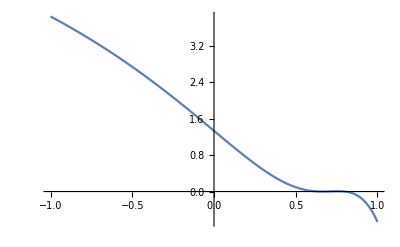

```mathematica
Plot[ pSquaredSol  , {γ,-1,1}]
```